# FitzHugh-Nagumo model for 2 coupled cells

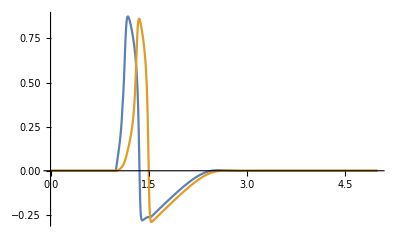

```mathematica
f[V_]:= V*(1-V)(V-a)
eqV1[V1_,w1_, V2_, w2_]:=1/ϵ*(-w1+ f[V1] + (V2-V1)/R +Iext[t])
eqw1[V1_,w1_, V2_, w2_]:=V1-γ*w1
eqV2[V1_,w1_, V2_, w2_]:=1/ϵ*(-w2+ f[V2] + (V1-V2)/R )
eqw2[V1_,w1_, V2_, w2_]:=V2-γ*w2

stimulus={WhenEvent[t==Subscript[T, on],Iext[t]->strength],WhenEvent[t==Subscript[T, off],Iext[t]->0.0]};
(*pars= {a->0.2, γ->0.4, ϵ->0.01, R->10.0, Subscript[T, on]->1, Subscript[T, off]-> 1.1, strength->0.1};*)
pars= {a->0.1, γ->0.5, ϵ->0.008, R->45.0, Subscript[T, on]->1, Subscript[T, off]-> 1.1, strength->0.025};
tmin=0;
tmax=5;

sys = {D[V1[t], t]==eqV1[V1[t], w1[t], V2[t], w2[t]], 
D[w1[t], t]==eqw1[V1[t], w1[t], V2[t], w2[t]],
D[V2[t], t]==eqV2[V1[t], w1[t], V2[t], w2[t]],
D[w2[t], t]==eqw2[V1[t], w1[t], V2[t], w2[t]]};
init = Thread[{V1[tmin], w1[tmin], V2[tmin], w2[tmin], Iext[tmin]}=={0, 0, 0, 0, 0}];
vars = {V1[t], w1[t], V2[t], w2[t]};

solution = NDSolve[{sys, init, stimulus}/.pars, vars, {t, tmin, tmax}, DiscreteVariables->Iext];

Plot[Evaluate[{V1[t], V2[t]}/.solution], {t, tmin,tmax}, PlotRange->All]
```